# Machine Learning

## Part 3: Feedforward Neural Nets

Yen Lee Loh, 2022-12-6

## Section General Theory of Neural Nets

### Section.Subsection Definitions

A graph consists of a set of vertices (nodes) connected by edges (links or bonds).
A digraph consists of a set of vertices connected by directed edges (arrows).

From now on, an artificial neural network will be referred to as a net.
A net is a graph consisting of nodes connected by layers.  A layer may consist of a single edge, or of any number of edges.  (See examples...)  
A net has one or more nodes that are inputs, and one or more nodes that are outputs.

A layer is a function that takes inputs and produces outputs.  Examples of layers include:
– elementwise layers (identity, tanh, sigmoid, ReLU/ramp, etc.)
– linear layers (dense linear layers corresponding to multiplication by a dense matrix)
– convolutional layers (linear layers corresponding to multiplication by a Toeplitz or circulant matrix)
– mean pooling layers (a type of linear layer)
– max pooling layers (which are nonlinear).
Linear layers and convolutional layers have special inputs called parameters.  Parameters are stored in the layer.  They are never taken directly from training data.  [[The same parameters are used for all inputs.]]] 
According to these definitions, a net is also a layer, and a layer is also a net.

It is often useful for the net to produce several outputs.  For example, a net for 10-way classification (for MNIST or CIFAR-10) may output the following:
– an integer Y ∈ (0, 1, 2, …, 9) representing the index of the most likely class (“dog”)
– an array of 10 real numbers {p_0,…,p_9}⊆[0,1] representing the probabilities of each class (70% dog, 20% cat, 10% horse, etc.)
– a loss value, representing the badness-of-fit for a training dataset, or the badness-of-prediction for a validation dataset

Training or learning means updating parameters in a way to reduce the total loss.

Nets are usually trained using backpropagation in combination with an optimizer.  (In PyTorch this is call the autograd mechanism.)  Backpropagation means using the chain rule to calculate derivatives of the loss (the output of the net) with respect to the parameters of the net (special inputs that reside within layers).

An optimizer is an algorithm that takes a parameter point w, a function value F , and the gradient ∇F (consisting of derivatives with respect to parameters w), and suggests an new guess for w.

In general, loss will be used to refer to a differentiable, real-valued function.  In contrast, accuracy or error may refer to the number of correctly classified examples, which is an integer, and thus is non-differentiable.

## Section Types of Layers

### Section.Subsection Elementwise layers

Any differentiable unary function can be used in an elementwise layer, which applies the function to each input to obtain each output, as shown in the sketch below.

-Graphics-

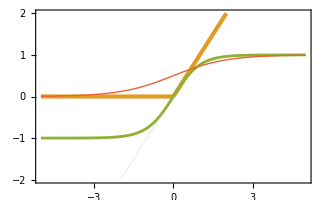

```mathematica
Plot[{Identity[x],Ramp[x],Tanh[x],1/(1+E^-x)},{x,-5,5},PlotLegends->"Expressions",PlotRange->{-2,2},PlotStyle->{AbsoluteThickness@0,AbsoluteThickness@3,AbsoluteThickness@2,AbsoluteThickness@1}]
```

The plot above shows functions that are often used as layers.
The identity function is a boring type of layer.  It represents a “jumper cable” that helps transmit signal from one point to another, but doesn’t process any information.

### Section.Subsection Loss layers

In principle, one may define layers that perform operations such as addition, subtraction, and multiplication on pairs of inputs.  However, binary operations are most commonly encountered in the final stage of a network, where one compares the model output and target output to obtain a loss value, as illustrated in the diagram below.

-Graphics-

Frameworks such as PyTorch provide implementations of loss functions such as MSELoss and BCELoss:
	F_MSE(Y,y)=(Y-y)^2
	F_BCE(Y,y)=(1+y)/2 ln 2/(1+Y) +(1-y)/2 ln 2/(1-Y) .

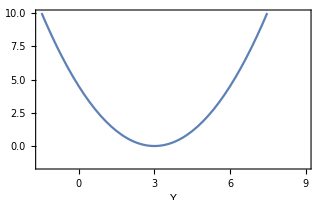
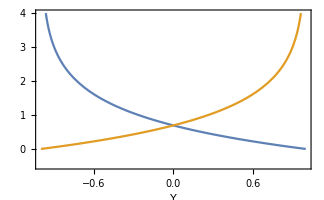

```mathematica
x=3;
Row@{
Plot[(y-x)^2/2,{y,-1.5,9},FrameLabel->{"Y",""},PlotRange->{-1.5,10},PlotRangePadding->0,PlotLegends->{"F"},Axes->True,AxesOrigin->{0,0}],Plot[{Log[2/(1+Y)],Log[2/(1-Y)]},{Y,-1,1},FrameLabel->{"Y",""},PlotRange->{-.5,4},PlotRangePadding->0.1,PlotLegends->{"F","F"},Axes->True,AxesOrigin->{0,0}]
}(*Export[NotebookDirectory[]<>"/Penalties.pdf",gr]*)
```

### Section.Subsection Linear layers

Given an input vector x̲, a linear layer outputs u̲=UnderBar[w̲] x̲+b̲ where the weight matrix UnderBar[w̲] and bias vector b̲ are parameters.  We may visualize these parameters as quantities

-Graphics- | -Graphics-

### Section.Subsection Convolutional layers

Given a set of inputs x̲, a convolutional layer outputs u̲=w̲⊗x̲+b where ⊗ represents a 1D, 2D, or 3D discrete convolution.  There are some details...

-Graphics-

### Section.Subsection Pooling layers (TBD)

### Section.Subsection Sequences of layers

One may combine layers to form chains or other structures.  For example:

-Graphics-

If the net is a digraph without cycles, then it is a feedforward neural network.  If cycles are present then one has a recurrent neural network (RNN).

## Section Linear Regression as a Neural Net

In Part 2: Generalized Linear Models, we saw that the cost function for a linear model is the chi-squared function
	F({y_n}|{x_n};w)=∑_(n=1)^N (y_n-w·x_n)^2
and that the mean and mode are both
	Y=w·x_n
	Y_mp=w·x_n.
We can represent this by the net below.

-Graphics-

In fact, we can train the net by backpropagation.  (But pointless since there is analytic solution)

## Section Logistic Regression as a Neural Net: The Single-Layer Perceptron (SLP)

https://en.wikipedia.org/wiki/Multilayer_perceptron#Activation_function

In Part 2: Generalized Linear Models, we saw that the cost function for a Bernoulli GLM (i.e., for logistic regression) is
	F({y_n}|{x_n};w)=∑_(n=1)^N f(y_n|Y_n),
	f(y|Y)=(1+y)/2 ln 2/(1+Y)+(1-y)/2 ln 2/(1-Y),
	Y_n=Y(x_n),
	Y(x)=tanh(w·x)/2.
Also,
	Y_mp(x)=sgn(w·x).
We can represent this Bernoulli GLM by a single-layer perceptron (SLP).  A SLP is a neural network that takes a D-dimensional input vector x, feeds it into a linear layer with one output, and feeds that output into a nonlinear function g called the activation function.  (This is supposed to mimic neurons in a real brain.)  For training purposes, the output of the SLP is fed into a loss function f to compare it with the training outputs.  If we choose g(u)=tanh u/2 and the binary cross-entropy (BCE) loss function f(y|Y)=(1+y)/2 ln 2/(1+Y)+(1-y)/2 ln 2/(1-Y), the resulting neural network is equivalent to a Bernoulli GLM.

-Graphics-

In principle, one could cut out the intermediate node Y  and combine the two operations u→Y and  Y→f into a single operation u→f.  However, I think there may not be a layer that directly implements the function  f=ln(1+e^-yu), so one would have to code this oneself.  There is no real advantage in doing this.  Moreover, the node Y is useful as a measure of confidence in the decision.

In other words:

SLP, GLM, and logistic regression are the same thing.

## Section Support Vector Classification as a Neural Net

Support vector classification can also be represented by a neural net.  The main difference is that in SVC it is not necessary, nor convenient, to work with the mean Y as an intermediate quantity.  Instead, one combines u and y directly into f=ramp(1-yu) with arithmetic operations only.  This makes feedforward and backpropagation faster.

-Graphics-

Suppose the training label is y=+1.  If u≫1, then Y_mp=+1, the classification is correct, and nothing happens.  If instead u≪-1, then Y_mp=-1!=y, the classification is wrong, and the loss is large.  Backpropagation increases the weights associated with bright pixels in the input — i.e., in future, when the net sees these pixels, it remembers that the class is supposed to be y=+1.

## Section Automatic Differentiation

To train a net efficiently, we need to be able to calculate the derivatives of the loss with respect to all parameters of the net.  This can be accomplished using automatic differentiation and backpropagation.

### Section.Subsection Example 1

Consider a tanh layer followed by a ramp layer:
	x⟶^tanh u⟶^ramp v.
Now
	u=tanh x	∴	du/dx=sech^2 x=1-u^2
	v=ramp u	∴	dv/du=Θ(u)=Θ(v).
For a given value of x, after calculating u and v in feedforward order, we can use the chain rule to obtain
	dv/dx=du/dx dv/du.

### Section.Subsection Example 2

Consider a multi-input single-output linear layer, followed by a tanh layer, followed by a BCELoss layer in which the second input is +1.  That is,
	x_j⟶^(∑_j w_j □)u⟶^tanh Y⟶^(BCELoss(□,+1))F.
Now
	u=∑_j w_j x_j	∴	(∂u)/(∂w_j)=x_j
	Y=tanh(u)	∴	dY/du=sech^2 u=1-Y^2
	F=ln 2/(1+Y)	∴	dF/dY=-1/(1+Y).
The chain rule gives
	(∂F)/(∂w_j)=(∂u)/(∂w_j)dY/du dF/dY=x_j(1-Y^2)(-1/(1+Y)).

To gain more insight, note that during training, the weight evolves according to (d w_j)/dt∝-(∂F)/(∂w_j)=x_j(1-Y).  If x_j>0, then w_j will tend to increase.  If there is only one training example, such as x_j=(+1,+1,-1,+1,-1), then we expect that the weights will end up something like (+9,+9,-9,+9,-9).

### Section.Subsection Example 3

Mulayer.........perceptron....... [TBD]
	y_i=∑_j w_ij x_j		∀i
	(∂y_k)/(∂w_ij)=δ_ki x_j
	(∂y_i)/(∂x_j)=w_ij
	(∂z_i)/(∂w_ij)=(d z_i)/(d y_i)(∂y_i)/(∂w_ij)=(1-z_i^2)x_j.

## Section Optimizers [TBD]

Mainly Stochastic Gradient Descent (SGD) and ADAM.

## Section Multi-Layer Perceptron (MLP)

GLMs and SLPs have a linear dependence on the inputs.  This makes it impossible for them to nonlinear learn functions like XOR.  Even though kernelized GLMs are nonlinear, they are still based on pattern recognition – comparison to known examples.  To demonstrate cognitive thinking, logical thinking, deduction, and ultimately artificial intelligence, a computer has to be able to do much more than pattern recognition.  This motivates us to explore deep learning architectures such as multi-layer neural networks.

### Section.Subsection Multi-Layer Perceptrons

From https://en.wikipedia.org/wiki/Multilayer_perceptron:

A multilayer perceptron (MLP) is a class of feedforward artificial neural network (ANN). The term MLP is used ambiguously, sometimes loosely to any feedforward ANN, sometimes strictly to refer to networks composed of multiple layers of perceptrons (with threshold activation). Multilayer perceptrons are sometimes colloquially referred to as “vanilla” neural networks, especially when they have a single hidden layer.

An MLP consists of at least three layers of nodes: an input layer, a hidden layer and an output layer. Except for the input nodes, each node is a neuron that uses a nonlinear activation function. MLP utilizes a supervised learning technique called backpropagation for training. Its multiple layers and non-linear activation distinguish MLP from a linear perceptron. It can distinguish data that is not linearly separable.

The term “multilayer perceptron” does not refer to a single perceptron that has multiple layers. Rather, it contains many perceptrons that are organized into layers. An alternative is “multilayer perceptron network”. Moreover, MLP “perceptrons” are not perceptrons in the strictest possible sense. True perceptrons are formally a special case of artificial neurons that use a threshold activation function such as the Heaviside step function. MLP perceptrons can employ arbitrary activation functions. A true perceptron performs binary classification, an MLP neuron is free to either perform classification or regression, depending upon its activation function.

The term “multilayer perceptron” later was applied without respect to nature of the nodes/layers, which can be composed of arbitrarily defined artificial neurons, and not perceptrons specifically. This interpretation avoids the loosening of the definition of “perceptron” to mean an artificial neuron in general.

Consider a problem with an input vector x and an output vector y (where the values may be real numbers in [-1,1]).  Consider a MLP with L layers.  For concreteness, let L=3.  The model function Y(x) is defined by a nested sequence of functions, Y=g(w^(2)·g(w^(1)·g(w^(0)·x))), where the nonlinear function g of a vector is understood to apply component-by-component.  Let us spell this out:
	Y≡x^(L)				(output vector is final layer of neurons),
	x_i^(l+1)=g(∑_j w_ij^(l)x_j^(l))	where l=0,1,2 is the layer index,
	x_i^(0)≡x_i				(input vector is first layer of neurons).
Here {w_ij^(l)} are weights connecting neurons in layer l to neurons in layer l+1.  g(z) is a sigmoid function.  The structure of the MLP is summarized below:

x≡x^(0)⟶^(g(w^(0)·…))x^(1)⟶^(g(w^(1)·…))x^(2)⟶^(g(w^(2)·…))x^(3)≡Y

The mathematics for the sigmoid function is so important that we will devote the next section to it.

### Section.Subsection Derivative identities for various sigmoid functions

#### g(z)=tanh z

g(z)=tanh z
∴	g'(z)=sech^2 z=1-tanh^2 z=1-(g(z))^2=h(g(z)) where h(g)=1-g^2.

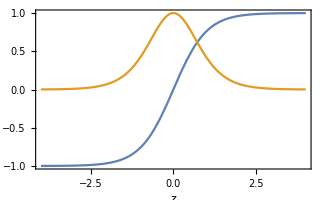
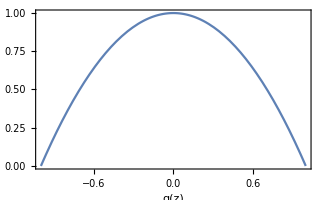

```mathematica
Row@{
Plot[{Tanh[z],Sech[z]^2},{z,-4,4},FrameLabel->{"z"},PlotLegends->Placed[{"g(z)","g'(z)"},{.8,.2}]],
Plot[{1-g^2},{g,-1,1},FrameLabel->{"g(z)"},PlotLegends->Placed[{"g'(z)"},{.8,.2}]]
}
```

#### g(z)=1/(1+e^-z)

Suppose we use a Fermi-Dirac function as the sigmoid function,
	g(z)=1/(1+e^-z).
The derivative of this function is
	g'(z)=e^z/((1+e^z)^2)
We may write the derivative of the function in terms of the value of the function instead:
	g'(z)=1/(1+e^-z)(1-1/(1+e^-z))=h(g(z)) where h(g)=g(1-g).

We can derive this directly as follows:
	g(z)=1/(1+e^-z)=1/2(1+tanh z/2)
∴	z=2arctanh(2g-1)
∴	(∂z)/(∂g)=1/(g(1-g))
∴	(∂g)/(∂z)=g(1-g).

#### g(z)=1/2+z/(2 √(1+z^2))

A similar result can be obtained for any other type of sigmoid function.  For example, suppose
	g(z)=1/2+1/2 z/(√(1+z^2))		∴	2g-1=z/(√(1+z^2)) ∴ (2g-1)^2(1+z^2)=z^2 ∴ (4 g^2-4g)z^2-(2g-1)^2=0 
∴	z=±√((2g-1)/(4g(g-1)))
∴	(∂z)/(∂g)=[some sleight of hand]				
∴	(∂g)/(∂z)=4(g^(3/2)(1-g))^(3/2).

```mathematica
g[z_]:=1/2+1/2 z/(√(1+z^2));
D[g[z], z]//FullSimplify
4(g[z]*(1-g[z]))^(3/2)//FullSimplify//PowerExpand
```

1/(2 (1+z^2)^(3/2))

1/(2 (1+z^2)^(3/2))

### Section.Subsection Backpropagation

Recall that
	x_i^(l+1)=g(∑_j w_ij^(l)x_j^(l)).
Take partial derivatives:
	(∂x_i^(l+1))/(∂w_ij^(l))=g'(∑_j w_ij^(l)x_j^(l))x_j^(l)=h(x_i^(l+1))x_j^(l),
	(∂x_i^(l+1))/(∂x_j^(l))=g'(∑_j w_ij^(l)x_j^(l))w_ij^(l)=h(x_i^(l+1))w_ij^(l).

Let the cost function be
	F=1/2∑_n ∑_i [x_ni^(3)-y_ni]^2=1/2∑_n ∑_i [ϵ_ni^(3)]^2
where n is the data point index and ϵ_ni^(3)=x_ni^(3)-y_ni.

We wish to minimize F({w_ij^(l)}) using gradient descent, so we need to be able to compute the derivatives of F with respect to all the weights.  Suppressing the n index for brevity,
	(∂F)/(∂w_ij^(2))=∑_n ϵ_i^(3)(∂ϵ_i^(3))/(∂w_ij^(2))		
		=∑_n ϵ_i^(3)(∂x_i^(3))/(∂w_ij^(2))=∑_n ϵ_i^(3)h(x_i^(3))x_j^(2)
	(∂F)/(∂w_jk^(1))=∑_ni ϵ_i^(3)(∂x_i^(3))/(∂x_j^(2))(∂x_j^(2))/(∂w_jk^(1))=∑_ni ϵ_i^(3)h(x_i^(3))w_ij^(2)h(x_j^(2))x_k^(1)	
	(∂F)/(∂w_kl^(0))=∑_nij ϵ_i^(3)(∂x_i^(3))/(∂x_j^(2))(∂x_j^(2))/(∂x_k^(1))(∂x_k^(1))/(∂w_kl^(0))=∑_nij ϵ_i^(3)h(x_i^(3))w_ij^(2)h(x_j^(2))w_jk^(1)h(x_k^(1))x_l^(0).

The derivatives above appear complicated, but we can write them in a simple form using “backpropagation”.  Let
	ϵ_i^(3)=x_i^(3)-y_i			δ_i^(3)=ϵ_i^(3)h(x_i^(3))
	ϵ_j^(2)=∑_i δ_i^(3)w_ij^(2)		δ_j^(2)=ϵ_j^(2)h(x_j^(2))
	ϵ_k^(1)=∑_j δ_j^(2)w_jk^(1)		δ_k^(1)=ϵ_k^(1)h(x_k^(1)).

Then
	(∂F)/(∂w_ij^(2))=∑_n δ_i^(3)x_j^(2)
	(∂F)/(∂w_jk^(1))=∑_ni δ_j^(2)x_k^(1)	
	(∂F)/(∂w_jk^(0))=∑_nj δ_k^(1)x_l^(0).

In principle, we may minimize F with respect to w, performing a sum over n for each derivative computation.

In practice, one considers the data points one by one as follows:

1.  Initialize {w_ij} randomly.  
2.  For each training data point n:
	– Given training inputs x_i^(0)≡x_i, compute neuron values x_i^(1),x_i^(2),x_i^(3) using feedforward equations.
	– Calculate level-3 error ϵ_i^(3)=x_i^(3)-y_i.
	– Calculate derivatives (∂F)/(∂w_ij^(l)) at all levels using backpropagation.
	– Update each weight using learning rule w_ij^(l):=w_ij^(l)-η(∂F)/(∂w_ij^(2)) with appropriate learning rate η.	
3.  Repeat step 2 (sweep through data again and again) until convergence.

### Section.Subsection Additional remarks

Each layer may have a different number of neurons, N^(l) (l=0,1,2,3).

In order to incorporate biases, one may include a “zeroth node” in each layer whose value is fixed at x_0^(l)=1, and let the index run from 0 to N^(l).

In our problem specification, we have allowed multiple outputs, N^(L)>1.  But ultimately, each output can be thought of as a separate function of the inputs.  So in principle one may break down the problem into scalar-output problems with N^(L)=1.

### Section.Subsection Simulation

The code below applies a 3-layer MLP to a dataset with number of data points N=6 and feature dimension D=3.  
This training dataset is easily learnable, because it corresponds to the function y=x_1+x_2+x_3.

```mathematica
(*-------- DEFINE TRAINING DATA SET --------*)
dataTrain=({{-1, 1, -1, -1}, {-1, -1, 1, -1}, {-1, -1, -1, 1}, {1, 1, 1, -1}, {1, 1, -1, 1}, {1, -1, 1, 1}});(* FIRST column is the training output y, OTHER cols are x *)
xndTrain=Rest/@dataTrain;
ynTrain=First/@dataTrain;
{nmax,dmax}=Dimensions@xndTrain;
```

```mathematica
(*-------- DEFINE NEURAL NETWORK AND INITIALIZE PARAMETERS --------*)
g[x_]:=Tanh[x];  (* sigmoid function whose output varies between -1 and +1 *)
h[g_]:=1-g^2;  (* derivative of sigmoid function as function of its value *)
eta=+0.2;  (* learning rate *)
m0=dmax; (* number of neurons in layer 0.  Should be equal to number of inputs, unless we use bias *)
m1=4;(* number of neurons in layer 1 *)
m2=3;(* number of neurons in layer 2 *)
m3=1;(* number of neurons in layer 3.  Should be equal to number of outputs. *)
w0=.2RandomReal[{-1,1},{m1,m0}];(* weights Subscript[w, ij]^(0) connecting layer 0 to layer 1 *)
w1=.2RandomReal[{-1,1},{m2,m1}];
w2=.2RandomReal[{-1,1},{m3,m2}];
```

```mathematica
(*-------- TRAIN NEURAL NETWORK USING TRAINING DATA SET --------*)
Do[(* loop over iterations ("passes" or "sweeps") *)
chiSquared=0.;
Do[ (* loop over training inputs *)
y={ynTrain⟦n⟧};  (* training output *)
x0=xndTrain⟦n⟧;(* set zeroth layer of neurons equal to training inputs *)
x1=g[w0.x0];(* feedforward *)
x2=g[w1.x1];(* feedforward *)
x3=g[w2.x2];(* feedforward *)
e3=x3-y;d3=e3*h[x3];(* calculate level-3 error and level-3 delta *)
e2=d3.w2;d2=e2*h[x2];(* backpropagate *)
e1=d2.w1;d1=e1*h[x1];(* backpropagate *)
w2-=eta*KroneckerProduct[d3,x2];(* update weights *)
w1-=eta*KroneckerProduct[d2,x1];
w0-=eta*KroneckerProduct[d1,x0];
chiSquared+=Norm[e3]^2/2;
,{n,nmax}];
If[Mod[iter,10]==0,Print["Iteration = ",iter,"   χ^2 = ",chiSquared]];
,{iter,0,100}];
```

Iteration = 0   χ^2 = 3.01384

Iteration = 10   χ^2 = 1.43815

Iteration = 20   χ^2 = 0.020433

Iteration = 30   χ^2 = 0.00872327

Iteration = 40   χ^2 = 0.0054042

Iteration = 50   χ^2 = 0.00387388

Iteration = 60   χ^2 = 0.00300232

Iteration = 70   χ^2 = 0.00244271

Iteration = 80   χ^2 = 0.00205436

Iteration = 90   χ^2 = 0.00176978

Iteration = 100   χ^2 = 0.00155265

```mathematica
(*-------- DISPLAY TABLE OF INPUTS AND OUTPUTS TO VERIFY ACCURACY --------*)
Table[
y=ynTrain⟦n⟧;  (* training output scalar *)
x0=xndTrain⟦n⟧;(* set zeroth layer of neurons equal to training inputs *)
x1=g[w0.x0];(* feedforward *)
x2=g[w1.x1];(* feedforward *)
x3=g[w2.x2];(* feedforward *)
Y=x3⟦1⟧//Round[#,0.001]&; (* predicted output scalar *)
{x0,"",y,Y}//Flatten
,{n,nmax}]//TableForm[#,TableHeadings->{None,{{"x_1","x_2","x_3"},"","y (train)","Y (pred)"}//Flatten}]&
```

x_1 | x_1 | x_3 |  | y (train) | Y (pred)
1 | -1 | -1 |  | -1 | -0.977
-1 | 1 | -1 |  | -1 | -0.977
-1 | -1 | 1 |  | -1 | -0.977
1 | 1 | -1 |  | 1 | 0.977
1 | -1 | 1 |  | 1 | 0.977
-1 | 1 | 1 |  | 1 | 0.977

### Section.Subsection Visualization of the above simulation

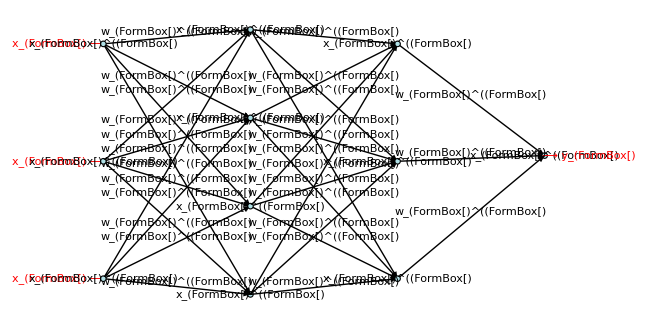

```mathematica
layers=3;
nodeCount={m0,m1,m2,m3};
nodePos[layer_,index_]:={layer,-((index-.51)/(nodeCount⟦1+layer⟧+.03))};
Graphics[{
Arrowheads[{{Medium,.5}}],
(*-------- Draw weights --------*)
Table[
Table[
{
Arrow@{nodePos[layer-1,j],nodePos[layer,i]},
Text[StringForm["w_(````)^(``)",i,j,layer-1],.5(nodePos[layer-1,j]+nodePos[layer,i]),{0,-1.2}]
}
,{j,1,nodeCount⟦layer⟧},{i,1,nodeCount⟦1+layer⟧}]
,{layer,1,layers}],
(*-------- Draw nodes --------*)
Table[
Table[
{
Inset[Graphics[{
(*-------- Draw node --------*)
FaceForm@RGBColor[.69,.878,.902],EdgeForm@Black,
Disk[{0,0},.3]
}],nodePos[layer,i],{0,0},.3]
,
Text[StringForm["x_(``)^(``)",i,layer],nodePos[layer,i]]
}
,{i,1,nodeCount⟦1+layer⟧}]
,{layer,0,layers}],
(*-------- Draw inputs/outputs --------*)
Red,
Table[
Text[StringForm["x_(``) ⟶",i],nodePos[0,i]+{-.3,0}]
,{i,1,nodeCount⟦1+0⟧}],
(*-------- Draw output(s) --------*)
Table[
Text[StringForm["⟶ y_(``)",i],nodePos[layers,i]+{+.3,0}]
,{i,1,nodeCount⟦1+layers⟧}]
},ImageSize->{648,324},AspectRatio->Full,PlotRangePadding->Scaled[.1]]
```

The above schematic shows a 3-level multilevel perceptron (MLP).  This is a kind of feedforward artificial neural network.

### Section.Subsection Animation of the training process for a MLP of the above simulation

Run all the cells below.

```mathematica
(*-------- DO THE NEXT STEP IN THE TRAINING PROCESS (EFFECTIVELY LOOPING OVER n AND iter) --------*)
nextStep[]:=Module[{},
If[nCurrent==nmax,iterCurrent++]; (* fake the Do loop *)
nCurrent=Mod[nCurrent+1,nmax,1]; (* fake the Do loop *)
y={ynTrain⟦nCurrent⟧};  (* training output *)
x0=xndTrain⟦nCurrent⟧;(* set zeroth layer of neurons equal to training inputs *)
x1=g[w0.x0];(* feedforward *)
x2=g[w1.x1];(* feedforward *)
x3=g[w2.x2];(* feedforward *)
e3=x3-y;d3=e3*h[x3];(* calculate level-3 error and level-3 delta *)
e2=d3.w2;d2=e2*h[x2];(* backpropagate *)
e1=d2.w1;d1=e1*h[x1];(* backpropagate *)
w2-=eta*KroneckerProduct[d3,x2];(* update weights *)
w1-=eta*KroneckerProduct[d2,x1];
w0-=eta*KroneckerProduct[d1,x0];
dw2=-eta*KroneckerProduct[d3,x2];(* for visualization purposes only *)
dw1=-eta*KroneckerProduct[d2,x1];(* for visualization purposes only *)
dw0=-eta*KroneckerProduct[d1,x0];(* for visualization purposes only *)
];
```

```mathematica
(*-------- DRAW --------*)
drawNode[pos_,color_,text_]:={
Inset[Graphics[{
(*-------- Draw node --------*)
FaceForm@color,EdgeForm@Black,
Disk[{0,0},.3]
}],pos,{0,0},.3]
,
Text[text,pos]
};
drawEdge[posStart_,posEnd_,val_]:={
colorFunc2@wlij⟦layer,i,j⟧,
AbsoluteThickness[9Tanh@Abs@wlij⟦layer,i,j⟧],
Arrow@{posStart,posEnd},
Text[fmt@wlij⟦layer,i,j⟧,.5(posStart+posEnd),{0,-1.2}]
};
drawEdgeChange[posStart_,posEnd_,color_,text_]:={
color,
Text[text,.5(posStart+posEnd),{0,+1.2}]
};
colorFunc[x_]:=Blend[{Red,Orange,Yellow,Green},Rescale[x,{-1,1}]];
colorFunc2[x_]:=Blend[{Red,Orange,Yellow,Darker@Green},Rescale[x,{-1,1}]];
fmt[x_]:=myFormat@Round[#,0.01]&@x;
fmt2[dw_]:=If[dw>0,"++","--"];
draw[]:=Module[{},
layers=3;
nodeCount={m0,m1,m2,m3};
xli={x0,x1,x2,x3};
wlij={w0,w1,w2};
dwlij={dw0,dw1,dw2};
nodePos[layer_,index_]:={layer,-((index-.51)/(nodeCount⟦1+layer⟧+.03))};
Return@Graphics[{
Arrowheads[{{Medium,.5}}],
(*-------- Draw weights --------*)
Table[
drawEdge[nodePos[layer-1,j],nodePos[layer,i],wlij⟦layer,i,j⟧]
,{layer,1,layers},{j,1,nodeCount⟦layer⟧},{i,1,nodeCount⟦1+layer⟧}],
(*-------- Draw CHANGES to weights based on backpropagation --------*)
Table[
drawEdgeChange[nodePos[layer-1,j],nodePos[layer,i],colorFunc2@Sign@dwlij⟦layer,i,j⟧,fmt2@dwlij⟦layer,i,j⟧]
,{layer,1,layers},{j,1,nodeCount⟦layer⟧},{i,1,nodeCount⟦1+layer⟧}],
(*-------- Draw nodes --------*)
Table[
drawNode[nodePos[layer,i],colorFunc@xli⟦1+layer,i⟧,fmt@xli⟦1+layer,i⟧]
,{layer,0,layers},{i,1,nodeCount⟦1+layer⟧}],
(*-------- Draw TRAINING OUTPUT and ERRORS --------*)
Table[{
drawNode[nodePos[layer,i]+{.6,0},colorFunc@y⟦i⟧,fmt@y⟦i⟧],
drawNode[nodePos[layer,i]+{.3,0},colorFunc@e3⟦i⟧,fmt@e3⟦i⟧],
Text[StringForm["y_(``)",i],nodePos[layer,i]+{0,0},{0,4}],
Text[StringForm["Y_(``)",i],nodePos[layer,i]+{.6,0},{0,4}],
Text[StringForm["ϵ_(``)",i],nodePos[layer,i]+{.3,0},{0,4}]
},{layer,{layers}},{i,1,nodeCount⟦1+layer⟧}],
(*-------- Draw inputs/outputs --------*)
Table[
Text[StringForm["x_(``) ⟶",i],nodePos[0,i]+{-.3,0}]
,{i,1,nodeCount⟦1+0⟧}]
},ImageSize->{648,324},AspectRatio->Full,PlotRangePadding->Scaled[.1],
PlotLabel->(StringForm["Iteration=``     Training example n=``",iterCurrent,nCurrent]//Style[#,Black]&)]
];
```

```mathematica
initNN[]:=Module[{},
(*-------- DEFINE TRAINING DATA SET --------*)
dataTrain=({{-1, 1, -1, -1}, {-1, -1, 1, -1}, {-1, -1, -1, 1}, {1, 1, 1, -1}, {1, 1, -1, 1}, {1, -1, 1, 1}});(* FIRST column is the training output y, OTHER cols are x *)
xndTrain=Rest/@dataTrain;
ynTrain=First/@dataTrain;
{nmax,dmax}=Dimensions@xndTrain;
(*-------- DEFINE NEURAL NETWORK AND INITIALIZE PARAMETERS --------*)
nCurrent=0;iterCurrent=1; (* pre-start*)
g[x_]:=Tanh[x];  (* sigmoid function whose output varies between -1 and +1 *)
h[g_]:=1-g^2;  (* derivative of sigmoid function as function of its value *)
eta=+0.2;  (* learning rate *)
m0=dmax; (* number of neurons in layer 0.  Should be equal to number of inputs, unless we use bias *)
m1=4;(* number of neurons in layer 1 *)
m2=2;(* number of neurons in layer 2 *)
m3=1;(* number of neurons in layer 3.  Should be equal to number of outputs. *)
w0=.2RandomReal[{-1,1},{m1,m0}];(* weights Subscript[w, ij]^(0) connecting layer 0 to layer 1 *)
w1=.2RandomReal[{-1,1},{m2,m1}];
w2=.2RandomReal[{-1,1},{m3,m2}];
];
```

```mathematica
(*-------- MAKE THE DEMO --------*)
DynamicModule[{gr},
initNN[];  (* initialize *)
nextStep[];gr=draw[]; (* go to the first iteration of the process *)
Print@Deploy@Panel@Column[{
Dynamic@gr,
Row@{
Button["Next step",nextStep[];gr=draw[];,ImageSize->160,Background->LightBlue],
Spacer@16,
Button["Skip 60 steps",Do[nextStep[],{60}];gr=draw[];,ImageSize->160,Background->LightBlue],
Spacer@16,
Button["Skip 600 steps",Do[nextStep[],{600}];gr=draw[];,ImageSize->160,Background->LightBlue]
}
},Alignment->Center];
FinishDynamic[];
];
```

Next stepSkip 60 stepsSkip 600 steps

The demo above shows a 3-layer neural network with 3 inputs and 1 output.  Click the “Next step” button and observe the following:
1.  A new training example is loaded into the input nodes (x_1,x_2,x_3).  The 6 training examples are used cyclically.
2.  The values of nodes in subsequent layers are calculated by the feedforward equations x^(l+1)=g(w·x^(l)).
     The weights w_ij are indicated using arrows.  (The weights are initially small random numbers.)
3.  The predicted output y_1 is compared with the training output Y_1 to obtain the error ϵ_1.
4.  The weight changes δ w_ij^(l)=-η   ∂F/∂w_ij^(l) are found using backpropagation.
     For example, if x_1^(2)>0 and ϵ_1>0, then the connection w_11^(2) is weakened (indicated by “– –”).
     Conversely, if x_1^(2)>0 and ϵ_1<0, then the connection w_11^(2) is strengthened (indicated by “+ +”).

For this particular example, the true function is y=x_1+x_2+x_3.  The weights should converge to some kind of fixed point after 100 iterations.  

	(TBD: Screenshot an example and explain why it works)

### Section.Subsection Animation of the training process for a MLP for learning a XOR function

Run all the cells below.

```mathematica
(*-------- DO THE NEXT STEP IN THE TRAINING PROCESS (EFFECTIVELY LOOPING OVER n AND iter) --------*)
nextStep[]:=Module[{},
If[nCurrent==nmax,iterCurrent++]; (* fake the Do loop *)
nCurrent=Mod[nCurrent+1,nmax,1]; (* fake the Do loop *)
y={ynTrain⟦nCurrent⟧};  (* training output *)
x0=xndTrain⟦nCurrent⟧;(* set zeroth layer of neurons equal to training inputs *)
x1=g[w0.x0];(* feedforward *)
x2=g[w1.x1];(* feedforward *)
x3=g[w2.x2];(* feedforward *)
e3=x3-y;d3=e3*h[x3];(* calculate level-3 error and level-3 delta *)
e2=d3.w2;d2=e2*h[x2];(* backpropagate *)
e1=d2.w1;d1=e1*h[x1];(* backpropagate *)
w2-=eta*KroneckerProduct[d3,x2];(* update weights *)
w1-=eta*KroneckerProduct[d2,x1];
w0-=eta*KroneckerProduct[d1,x0];
dw2=-eta*KroneckerProduct[d3,x2];(* for visualization purposes only *)
dw1=-eta*KroneckerProduct[d2,x1];(* for visualization purposes only *)
dw0=-eta*KroneckerProduct[d1,x0];(* for visualization purposes only *)
];
```

```mathematica
(*-------- DRAW --------*)
drawNode[pos_,color_,text_]:={
Inset[Graphics[{
(*-------- Draw node --------*)
FaceForm@color,EdgeForm@Black,
Disk[{0,0},.3]
}],pos,{0,0},.3]
,
Text[text,pos]
};
drawEdge[posStart_,posEnd_,val_]:={
colorFunc2@wlij⟦layer,i,j⟧,
AbsoluteThickness[9Tanh@Abs@wlij⟦layer,i,j⟧],
Arrow@{posStart,posEnd},
Text[fmt@wlij⟦layer,i,j⟧,.5(posStart+posEnd),{0,-1.2}]
};
drawEdgeChange[posStart_,posEnd_,color_,text_]:={
color,
Text[text,.5(posStart+posEnd),{0,+1.2}]
};
colorFunc[x_]:=Blend[{Red,Orange,Yellow,Green},Rescale[x,{-1,1}]];
colorFunc2[x_]:=Blend[{Red,Orange,Yellow,Darker@Green},Rescale[x,{-1,1}]];
fmt[x_]:=myFormat@Round[#,0.01]&@x;
fmt2[dw_]:=If[dw>0,"++","--"];
draw[]:=Module[{},
layers=3;
nodeCount={m0,m1,m2,m3};
xli={x0,x1,x2,x3};
wlij={w0,w1,w2};
dwlij={dw0,dw1,dw2};
nodePos[layer_,index_]:={layer,-((index-.51)/(nodeCount⟦1+layer⟧+.03))};
Return@Graphics[{
Arrowheads[{{Medium,.5}}],
(*-------- Draw weights --------*)
Table[
drawEdge[nodePos[layer-1,j],nodePos[layer,i],wlij⟦layer,i,j⟧]
,{layer,1,layers},{j,1,nodeCount⟦layer⟧},{i,1,nodeCount⟦1+layer⟧}],
(*-------- Draw CHANGES to weights based on backpropagation --------*)
Table[
drawEdgeChange[nodePos[layer-1,j],nodePos[layer,i],colorFunc2@Sign@dwlij⟦layer,i,j⟧,fmt2@dwlij⟦layer,i,j⟧]
,{layer,1,layers},{j,1,nodeCount⟦layer⟧},{i,1,nodeCount⟦1+layer⟧}],
(*-------- Draw nodes --------*)
Table[
drawNode[nodePos[layer,i],colorFunc@xli⟦1+layer,i⟧,fmt@xli⟦1+layer,i⟧]
,{layer,0,layers},{i,1,nodeCount⟦1+layer⟧}],
(*-------- Draw TRAINING OUTPUT and ERRORS --------*)
Table[{
drawNode[nodePos[layer,i]+{.6,0},colorFunc@y⟦i⟧,fmt@y⟦i⟧],
drawNode[nodePos[layer,i]+{.3,0},colorFunc@e3⟦i⟧,fmt@e3⟦i⟧],
Text[StringForm["y_(``)",i],nodePos[layer,i]+{0,0},{0,4}],
Text[StringForm["Y_(``)",i],nodePos[layer,i]+{.6,0},{0,4}],
Text[StringForm["ϵ_(``)",i],nodePos[layer,i]+{.3,0},{0,4}]
},{layer,{layers}},{i,1,nodeCount⟦1+layer⟧}],
(*-------- Draw inputs/outputs --------*)
Table[
Text[StringForm["x_(``) ⟶",i],nodePos[0,i]+{-.3,0}]
,{i,1,nodeCount⟦1+0⟧}]
},ImageSize->{648,324},AspectRatio->Full,PlotRangePadding->Scaled[.1],
PlotLabel->(StringForm["Iteration=``     Training example n=``",iterCurrent,nCurrent]//Style[#,Black]&)]
];
```

```mathematica
initNN[]:=Module[{},
(*-------- DEFINE TRAINING DATA SET --------*)
dataTrain=({{1, 1, 1, 1}, {1, -1, 1, -1}, {1, -1, -1, 1}, {1, 1, 1, -1}, {-1, 1, -1, 1}, {-1, -1, 1, 1}, {-1, 1, 1, -1}, {-1, -1, -1, -1}});(* FIRST column is the training output y, OTHER cols are x *)
xndTrain=Rest/@dataTrain;
ynTrain=First/@dataTrain;
{nmax,dmax}=Dimensions@xndTrain;
(*-------- DEFINE NEURAL NETWORK AND INITIALIZE PARAMETERS --------*)
nCurrent=0;iterCurrent=1; (* pre-start*)
g[x_]:=Tanh[x];  (* sigmoid function whose output varies between -1 and +1 *)
h[g_]:=1-g^2;  (* derivative of sigmoid function as function of its value *)
eta=+0.2;  (* learning rate *)
m0=dmax; (* number of neurons in layer 0.  Should be equal to number of inputs, unless we use bias *)
m1=5;(* number of neurons in layer 1 *)
m2=4;(* number of neurons in layer 2 *)
m3=1;(* number of neurons in layer 3.  Should be equal to number of outputs. *)
w0=.2RandomReal[{-1,1},{m1,m0}];(* weights Subscript[w, ij]^(0) connecting layer 0 to layer 1 *)
w1=.2RandomReal[{-1,1},{m2,m1}];
w2=.2RandomReal[{-1,1},{m3,m2}];
];
```

```mathematica
(*-------- MAKE THE DEMO --------*)
DynamicModule[{gr},
initNN[];  (* initialize *)
nextStep[];gr=draw[]; (* go to the first iteration of the process *)
Print@Deploy@Panel@Column[{
Dynamic@gr,
Row@{
Button["Next step",nextStep[];gr=draw[];,ImageSize->160,Background->LightBlue],
Spacer@16,
Button["Skip 60 steps",Do[nextStep[],{60}];gr=draw[];,ImageSize->160,Background->LightBlue],
Spacer@16,
Button["Skip 600 steps",Do[nextStep[],{600}];gr=draw[];,ImageSize->160,Background->LightBlue]
}
},Alignment->Center];
FinishDynamic[];
];
```

Next stepSkip 60 stepsSkip 600 steps

The demo above shows a 3-layer neural network with 3 inputs and 1 output.  Click the “Next step” button and observe the following:
1.  A new training example is loaded into the input nodes (x_1,x_2,x_3).  The 6 training examples are used cyclically.
2.  The values of nodes in subsequent layers are calculated by the feedforward equations x^(l+1)=g(w·x^(l)).
     The weights w_ij are indicated using arrows.  (The weights are initially small random numbers.)
3.  The predicted output y_1 is compared with the training output Y_1 to obtain the error ϵ_1.
4.  The weight changes δ w_ij^(l)=-η   ∂F/∂w_ij^(l) are found using backpropagation.
     For example, if x_1^(2)>0 and ϵ_1>0, then the connection w_11^(2) is weakened (indicated by “– –”).
     Conversely, if x_1^(2)>0 and ϵ_1<0, then the connection w_11^(2) is strengthened (indicated by “+ +”).

This example is VERY hard to learn.... it’s a full XOR... and I think it tends to get stuck in local minima

## Section Convolutional Neural Networks (CNNs) – TBD

## Initialization cells

### Section.Subsection Basics

```mathematica
Solid=Dashing@{};
DarkGreen=Darker[Green,0.67];
resistorColorList={Black,Brown,Red,Orange,Darker@Yellow,Darker@Green,Blue,Purple,Gray,Cyan};
resistorStyle[n_Integer]:={AbsoluteThickness@1,resistorColorList[[Mod[n,Length@resistorColorList,1]]]};
purpleWhite[v_]:=Hue[0.75,0.25,Abs[v]^0.5];
blueWhiteRed[v_]:=Hue[If[v>0.5,0.0,0.5],(2Abs[v-0.5]),0.95];
colorFromComplex[z_,OptionsPattern[{Brightness->1.}]]:=Hue[Rescale[Arg@z,{0,2 π}],0.8,1-1/(1+Abs[z*OptionValue[Brightness]])];
enlargeFont=#/.s_String->Style[s,16]&;
myCF=Blend[{
Hue[0.8,0.75,0.75],
Hue[0.7,0.75,0.80],
Hue[0.6,0.75,0.90],
Hue[0.6,0.25,1.00],
White,
RGBColor[0.9938925000000001,0.989345,0.5766145],
RGBColor[0.955963,0.863115,0.283425],
RGBColor[0.881316,0.5539655,0.2226795],
RGBColor[0.817319,0.134167,0.164218]},
Clip[#,{0,1}]]&;
myCF=Blend[{
Hue[0.67,0.75,0.80],
White,
Hue[.15,.75,.80]},
Clip[#,{0,1}]]&;
```

```mathematica
myGS={BaseStyle->{14,FontFamily->"Times",Black}};
myPS={LabelStyle->{14,FontFamily->"Times",Black},ImageSize->324,RotateLabel->False,Frame->True,FrameStyle->Directive@{AbsoluteThickness@0,Black},ImageMargins->1};
myPS1={PlotStyle->ColorData[97]};
SetOptions[Graphics,myGS];
SetOptions[Plot,myGS,myPS,ExclusionsStyle->Automatic];
SetOptions[ParametricPlot,myGS,myPS,ExclusionsStyle->Automatic];
SetOptions[ListPlot,myGS,myPS,myPS1];
SetOptions[ListLinePlot,myGS,myPS,myPS1];
SetOptions[ListLogPlot,myGS,myPS];
SetOptions[ListLogLogPlot,myGS,myPS];
SetOptions[ListLogLinearPlot,myGS,myPS];
SetOptions[DiscretePlot,myGS,myPS];
SetOptions[RectangleChart,myGS,myPS];
SetOptions[ArrayPlot,myGS,myPS,AspectRatio->Automatic,PlotRangePadding->0];
SetOptions[ContourPlot,myGS,myPS,AspectRatio->Automatic,PlotRangePadding->0];
SetOptions[DensityPlot,myGS,myPS,AspectRatio->Automatic,PlotRangePadding->0];
SetOptions[StreamPlot,myGS,myPS,AspectRatio->Automatic,StreamColorFunction->None,StreamStyle->AbsoluteThickness@1];
SetOptions[Graphics3D,PlotRange->All,ImageSize->600,ViewPoint->{-1,-2,1},ViewVertical->{0,0,1},Lighting->"Neutral",Boxed->False,AspectRatio->Automatic];
```

### Section.Subsection Dimension lines (relatively new code: 2021-2-16)

```mathematica
(*---- USER MAY WANT TO TWEAK ARROWSIZE ----*)
dimLine[r1_,r2_,label_,tickLen_,arrowOffset_,labelOffset_]:=Module[{p,u,v,w,
arrowSize=0.015,
grAH=
Graphics[Line@{{-1,.3},{0,0},{-1,-.3}}]
(*Graphics[Polygon@{{-1,.5},{0,0},{-1,-.5}}]*)
},
p=r2-r1;u=Normalize@{-p⟦2⟧,p⟦1⟧};p=Normalize@p;
(*-------- CHECK IF DIMENSION IS SUFFICIENTLY LARGE --------*)
If[
Norm[r2-r1]>.8    (*5Max[tickLen,arrowOffset,labelOffset]*)
,
(*-------- ORDINARY INTERIOR DIMENSION LINE --------*)
{
Arrowheads[{{-arrowSize,Automatic,grAH},{arrowSize,Automatic,grAH}}],Arrow@{r1+arrowOffset*u,r2+arrowOffset*u},
Line@{{r1,r1+tickLen*u},{r2,r2+tickLen*u}},
Text[label,.55r1+.45r2+labelOffset*u]
},
(*-------- SPECIAL EXTERIOR DIMENSION LINE --------*)
{
exteriorLength=1;
Arrowheads[{{arrowSize,Automatic,grAH}}],
Arrow@{r2+exteriorLength*p+arrowOffset*u,r2+arrowOffset*u},
Arrow@{r1-exteriorLength*p+arrowOffset*u,r1+arrowOffset*u},
Line@{{r1,r1+tickLen*u},{r2,r2+tickLen*u}},
Text[label,.55r1+.45r2+labelOffset*u]
}
]
];
groundSymbol[{x_,y_},s_]:=(
Line@{{{0,3},{0,6}},{{-3,3},{3,3}},{{-2,2},{2,2}},{{-1,1},{1,1}}}
)//Translate[#,{0,-6}]&//Scale[#,s,{0,0}]&//Translate[#,{x,y}]&;
```

### Section.Subsection myFormat

```mathematica
(*-------- Pretty-print any real number --------*)
myFormat[v_]:=(
Which[
(*---- If v is an exact power of 10 with an exponent less than -4 or greater than +4, display v as 10^w ----*)
v>0&&Abs@Log10@v>5&&FractionalPart[Log10@v]==0,SuperscriptBox[10,Round@Log10@v],
(*---- If v is an integer, display v without any decimal points ----*)
Abs[v-Round@v]<10^-8,Round@v,
(*---- If v is not an integer, display v with decimals and possibly in scientific notation ----*)
True,NumberForm[N@v,ExponentFunction->(If[-4<#<4,Null,#]&),NumberPoint->"."]
](*//Style[#,FontWeight->Bold]&*));
```

### Section.Subsection Axis utilities: divisions, etc.

Let v be the numerical part of a physical quantity, and let x be the coordinate along the axis on which this quantity is plotted.
For example, suppose we are displaying 200 GHz at coordinate 8.3.  Then v=200×10^11 and x=8.3.
We will supply a conversion function vfromx to the myAxis function.

```mathematica
(*-------- Plotting parameters --------*)
maxMajorDivisions=30;
maxMinorDivisions=300;
tickLengthMajorP=0.25;
tickLengthMajorM=0.;
tickLengthMinorP=0.15;
tickLengthMinorM=0.;
textOffset=1.5;
(*-------- Round up or down to closest number in a list --------*)
roundUp[x_,xlist_]:=Min@Select[xlist,#≥x&];
roundDn[x_,xlist_]:=Max@Select[xlist,#≤x&];
(*-------- Round up or down to the nearest number of the form 1×10^n, 2×10^n, or 5×10^n --------*)
roundUpNicely[x_]:=Module[{expon},expon=Floor@Log10[x];roundUp[x/10^expon,{1,2,5,10}]*10^expon];
roundDnNicely[x_]:=Module[{expon},expon=Floor@Log10[x];roundDn[x/10^expon,{1,2,5,10}]*10^expon];
(*-------- Divide an interval to find a nice set of tick values --------*)
divisions[{vmin_,vmax_},maxDivisions_]:=Module[{vrange,vstep,vstart,lmin,lmax,v,divs},
vrange=vmax-vmin;
vstep=roundUpNicely[vrange/maxDivisions];
vstart=vstep*Ceiling[vmin/vstep];
divs=Select[Range[vstart,vmax,vstep],vmin≤#≤vmax&];
Return@divs;
];
(*-------- Divide an interval to find nice major and minor tick values --------*)
divisions[{vmin_,vmax_},{maxMajorDivisions_,maxMinorDivisions_}]:=Module[{vrange,vstep,vstart,lmin,lmax,v,majDivs,minDivs},
vrange=vmax-vmin;
vstep=roundUpNicely[vrange/maxMajorDivisions]; (* major division spacing *)
vstart=vstep*Ceiling[vmin/vstep];
majDivs=Select[Range[vstart,vmax,vstep],vmin≤#≤vmax&];
vstep=roundUpNicely[vstep/maxMinorDivisions]; (* minor division spacing *)
vstart=vstep*Ceiling[vmin/vstep];
minDivs=Select[Range[vstart,vmax,vstep],vmin≤#≤vmax&];
minDivs=Complement[minDivs,majDivs];
Return@{majDivs,minDivs}];
(*-------- Divide an interval with major ticks as 10^n and minor ticks as {2,3,4,5,6,7,8,9}×10^n --------*)
(*-------- This works well except when we have a very small interva --------*)
logDivisions[{vmin_,vmax_}]:=Module[{lmin,lmax,v,majDivs,minDivs}, (* l===Log10[v] *)
lmin=Floor@Log10@vmin;
lmax=Ceiling@Log10@vmax;
majDivs=Table[v=10^l;If[vmin≤v≤vmax,Sow@v],{l,lmin,lmax}]//Reap//Last//Last;
minDivs=Table[v=10^l*mantissa;If[vmin≤v≤vmax,Sow@v],{l,lmin,lmax},{mantissa,2,9}]//Reap//Last//Last;
Return@{majDivs,minDivs}];
linScale[label_,{xmin_,xmax_},vx_]:=Module[{vmin,vmax,xv,x},
xv=InverseFunction[vx];
{vmin,vmax}=Sort@(vx/@{xmin,xmax});
{vlist,vlist2}=divisions[{vmin,vmax},{30,6}];
vlist2=Flatten@vlist2;
Graphics[{
(*-------- Draw axis line and axis label --------*)
Text[label,{xmin,0},{2.00,0}],
{Line@{{xmin,0},{xmax,0}}},
(*-------- Draw major and minor tick marks --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMajorM},{x,tickLengthMajorP}}],{v,vlist}],
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMinorM},{x,tickLengthMinorP}}],{v,vlist2}],
(*-------- Draw major tick labels --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Text[v//myFormat//DisplayForm,{x,0},{0,textOffset}]],{v,vlist}]
},
PlotRange->{{xmin,xmax},{-.5,.5}},PlotRangePadding->{{Scaled@.05,Scaled@.01},{0,0}},
ImageSize->{1200,50},AspectRatio->Full,BaseStyle->{18,FontFamily->"Times"}]
];
logScale[label_,{xmin_,xmax_},vx_]:=Module[{vmin,vmax,xv,x},
xv=Quiet@InverseFunction[vx];
{vmin,vmax}=Sort@(vx/@{xmin,xmax});
{vlist,vlist2}=myLogDivisions[{vmin,vmax}];vlist2=Flatten@vlist2;
(*-------- Draw axis line and axis label --------*)
Graphics[{
Text[label,{xmin,0},{2.00,0}],
Line@{{xmin,0},{xmax,0}},
(*-------- Draw major and minor tick marks --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMajorM},{x,tickLengthMajorP}}],{v,vlist}],
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMinorM},{x,tickLengthMinorP}}],{v,vlist2}],
(*-------- Draw major tick labels --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Text[v//myFormat//DisplayForm,{x,0},{0,textOffset}]],{v,N@vlist}]
},
PlotRange->{{xmin,xmax},{-.5,.5}},PlotRangePadding->{{Scaled@.05,Scaled@.01},{0,0}},
ImageSize->{1200,50},AspectRatio->Full,BaseStyle->{18,FontFamily->"Times"}]
];
mark[x_,label_]:=Module[{},
{Line@{{x,-10},{x,-.5}},
Text[label,{x,-.5}]}
];
 stackScales[grList_]:=Module[{nmax=Length@grList},
Graphics[{
Table[
(*Inset[grList⟦n⟧,{0,-n}]*)
Translate[grList⟦n⟧⟦1⟧,{0,-n}]
,{n,nmax}],
},
ImageSize->{1200,50*nmax},AspectRatio->Full,
PlotRange->{All,{-nmax-.7,-.1}}
]
]
makeLabeledTicks[xmin_,xmax_]:=Module[{xMajorTicks,xMinorTicks,nMajorTicks=10,nMinorTicks=5,func=myFormat},
{xMajorTicks,xMinorTicks}=divisions[{xmin,xmax},{nMajorTicks,nMinorTicks}];
Join[
{N@#,func@#,{.02,0}}&/@xMajorTicks,
{N@#,Null,{.01,0}}&/@xMinorTicks
]
];
makeUnlabeledTicks[xmin_,xmax_]:=Module[{xMajorTicks,xMinorTicks,nMajorTicks=10,nMinorTicks=5,func=Null&},
{xMajorTicks,xMinorTicks}=divisions[{xmin,xmax},{nMajorTicks,nMinorTicks}];
Join[
{N@#,func@#,{.02,0}}&/@xMajorTicks,
{N@#,Null,{.01,0}}&/@xMinorTicks
]
];
```

### Section.Subsection autoTicksLabeled, etc.

```mathematica
decimalExponent[x_]:=Floor@Log10[x];
decimalMantissa[x_]:=x/(10^Floor@Log10[x]);
roundUpNicely[x_]:=SelectFirst[{1,2,5,10},#≥decimalMantissa[x]&]*10^decimalExponent[x];
divisions[{xmin_,xmax_},xstep_]:=Range[Ceiling[xmin,xstep],xmax,xstep]//Select[#,xmin≤#≤xmax&]&;
```

```mathematica
autoTicks$TickColor=White; (* MAY NEED TO SET THIS THING *)
autoTicksLabeled[xmin_,xmax_,nMajorTicks_:20,majorTickLen_:0.03,minorTickLen_:0.02]:=Module[{majorTicks,minorTicks},
majorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks]];
minorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks/5]]~Complement~majorTicks;
Join[{#,myFormat@N@#,{majorTickLen,0},autoTicks$TickColor}&/@majorTicks,{#,,{minorTickLen,0},autoTicks$TickColor}&/@minorTicks]
];
autoTicksUnlabeled[xmin_,xmax_,nMajorTicks_:20,majorTickLen_:0.03,minorTickLen_:0.02]:=Module[{majorTicks,minorTicks},
majorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks]];
minorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks/5]]~Complement~majorTicks;
Join[{#,,{majorTickLen,0},autoTicks$TickColor}&/@majorTicks,{#,,{minorTickLen,0},autoTicks$TickColor}&/@minorTicks]
];
autoContours=Function[{zmin,zmax},FindDivisions[{zmin,zmax},50]];
```

### Section.Subsection timeIt

```mathematica
SetAttributes[timeIt,HoldAll];
timeIt[cmds_]:=Module[{report,absTime,cpuTime},
report=AbsoluteTiming[Timing[cmds;]];
absTime=report⟦1⟧;
cpuTime=report⟦2,1⟧;
Print[StringForm["Absolute time = ``    CPU time = ``",absTime//DecimalForm[#,3]&,cpuTime//DecimalForm[#,3]&]]
];
```

### Section.Subsection myRealPlot and myComplexPlot

```mathematica
myRealPlot[xi_,yj_,zij_,opts:OptionsPattern[ArrayPlot]]:=Module[{},
gr=ArrayPlot[
Reverse@Transpose@zij,
opts,
DataRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},
PlotRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},PlotRangePadding->0,
ColorFunction->colorFromComplex,ColorFunctionScaling->False,
Frame->True,FrameTicks->{{autoTicksLabeled[#1,#2,10,.02,.01]&,autoTicksUnlabeled[#1,#2,10,.02,.01]&},{autoTicksLabeled,autoTicksUnlabeled}},
ImageSize->{648,216},AspectRatio->Full]
];
```

```mathematica
myComplexPlot[xi_,yj_,zij_,opts:OptionsPattern[ArrayPlot]]:=Module[{},
gr=ArrayPlot[
Reverse@Transpose@zij,
opts,
DataRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},
PlotRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},PlotRangePadding->0,
ColorFunction->colorFromComplex,ColorFunctionScaling->False,
Frame->True,FrameTicks->{{autoTicksLabeled[#1,#2,10,.02,.01]&,autoTicksUnlabeled[#1,#2,10,.02,.01]&},{autoTicksLabeled,autoTicksUnlabeled}},
ImageSize->{648,216},AspectRatio->Full]
];
```